```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=24;
Ly=24;
A=Lx*Ly;
```

```mathematica
m0 = 0.5;
```

```mathematica
(**-----------------Define the sine and cosine matrices--------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

1152

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+4
```

```mathematica
(**-------Rational-------**)
```

```mathematica
(** LineUp[x_]:=(2/3)(x-1)+8
LineDn[x_]:=(2/3)*(x-2)+4 **)
```

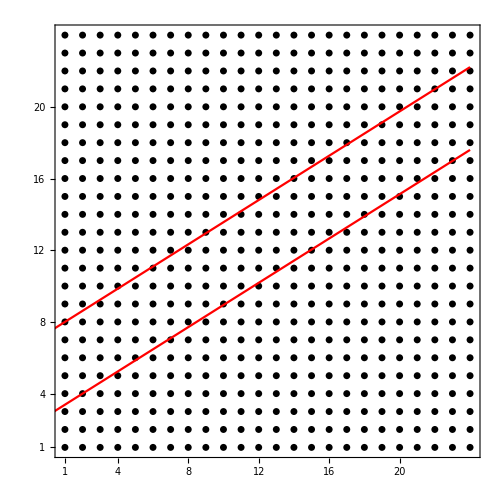

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
(** Site indices of the sites in the projected brane **)
```

```mathematica
Fibonlist=Sort[FibonupNew];
```

```mathematica
(** List of Y coordinates of the sites in the projected brane **)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
(** List of X coordinates of the sites in the projected brane **)
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(** Repeat the coordinates for the two onsite orbitals **)
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
(** This list contains (original) indices of the orbitals within the projected brane **)
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsBrane=Dimensions[TotalFibon][[1]]
```

220

```mathematica
NOrbitalsBrane/2
```

110

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsBrane
```

932

```mathematica
(** Percentage of sites within the Brane **)
```

```mathematica
Percentage = N[NOrbitalsBrane/(2*A)]
```

0.190972

```mathematica
(*-------------F1 is the list of all orbitals in the parent lattice. a is the list of orbitals outside the brane -----------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{1152}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------Create matrices for the Hamiltonian of the projected brane-------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,m0,1.0];
```

```mathematica
(*---------------This is H11-----------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsBrane}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}];
```

```mathematica
(*--------------------This is H22-----------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------This is H21------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsBrane}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsBrane}];
```

```mathematica
(*------------------This is H12------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
(** This is the effective Hamiltonian HPTB, defined in Eq. 1 in our paper **)
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(** To save memory, I delete some matrices which I no longer need **)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
(** --------------------------------------------------------- **)
```

```mathematica
(**-----------Diagonalize HPTB----------------**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsBrane}]//Chop;
```

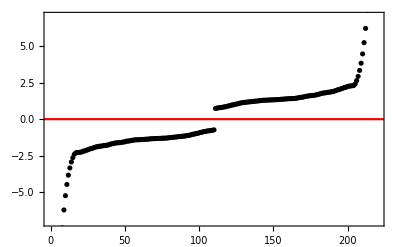

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-10,NOrbitalsBrane+10},PlotStyle-> Red]]
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsBrane}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

0

```mathematica
(** Real space Chern number calculation as per PHYSICAL REVIEW B 84,241106(R) (2011) **)
```

```mathematica
FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsBrane/2}];
```

```mathematica
Clear[P,Q,ChernMatrix,ChernMatrixDiagonalList,ChernMatrixSiteWiseList]
```

```mathematica
(** We create a projector P on the space of filled eigenstates (half-filling limit) **)
```

```mathematica
P = Table[0,{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsBrane/2}];
```

```mathematica
Dimensions[P]
```

{220,220}

```mathematica
Q =  IdentityMatrix[NOrbitalsBrane] - P;
```

```mathematica
percentageOfOrbitalsInside = N[NOrbitalsBrane/(2*A)]
```

0.190972

```mathematica
NSitesInside = NOrbitalsBrane/2
```

110

```mathematica
X1 = DiagonalMatrix[XListKron];
```

```mathematica
Y1 = DiagonalMatrix[YListKron];
```

```mathematica
Max[Abs[P.Q]]
```

4.31218×10^-14

```mathematica
(** Define the local Chern operator **)
```

```mathematica
ChernMatrix=-4π Im[(P.X1.Q.Y1.P)];
```

```mathematica
(** This is the Wanneir orbitalwise list **)
```

```mathematica
ChernMatrixDiagonalList= Diagonal[ChernMatrix];
```

```mathematica
(** Here I take two elements of the list at a time to add the contribution of both onsite orbitals **)
```

```mathematica
ChernMatrixSiteWiseList = Table[ChernMatrixDiagonalList[[2 i]]+ChernMatrixDiagonalList[[2i-1]],{i,1,NOrbitalsBrane/2}];
```

```mathematica
(**------------------------Here I export the list------------------------**)
```

```mathematica
Clear[location,filename,filenameString1,filenameString2,filenameString3,filenameString4,filenameString5,filenameString6]
```

```mathematica
location="dataPTB/";
```

```mathematica
filenameString1 = "dataPTBlocalChernLx=";
filenameString2="Ly=";
filenameString3 = "m0=";
filenameString4 = "Xup=";
filenameString5 = "Xdn=";
percentageString = "PartsPerThousand=";
```

```mathematica
(** This part checks whether the slope is rational/irrational **)
```

```mathematica
slope = D[LineUp[x],x];
If[Element[slope,Rationals]==True,filenameString6="Rational",filenameString6="Irrational"];
```

```mathematica
(** Finally, we create the filename **)
```

```mathematica
filename = StringJoin[location,filenameString1,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m0],filenameString4,ToString[LineUp[1]],filenameString5,ToString[LineDn[2]],percentageString,ToString[Round[percentageOfOrbitalsInside * 1000]],filenameString6,".dat"]
```

dataPTB/dataPTBlocalChernLx=24Ly=24m0=0.5Xup=8Xdn=4PartsPerThousand=191Irrational.dat

```mathematica
(** Here we export the file **)
```

```mathematica
Export[filename,ChernMatrixSiteWiseList];
```

```mathematica
(**----------------------------------------------------------------------------------------**)
```

```mathematica
(**----------------------------------------------------------------------------------------**)
```

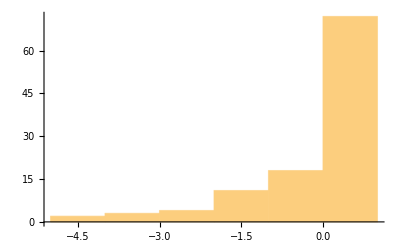

```mathematica
Histogram[ChernMatrixSiteWiseList]
```

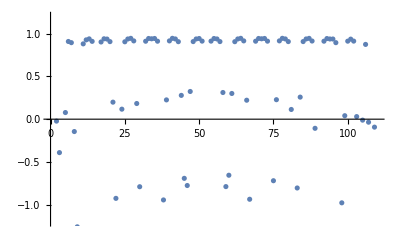

```mathematica
ListPlot[ChernMatrixSiteWiseList,PlotRange->{-1.2,1.2}]
```

```mathematica
Mean[ChernMatrixSiteWiseList]
```

1.43723×10^-15